```mathematica
plotstuff[a_]:=
(Graphics[{Circle[#[[1]],0.5],Text[#[[2]],#[[1]]]}&/@({Partition[a,2],Table[ToString[k],{k,1,7}]}//Transpose)]);
plotstuffsized[a_,size_]:=Image[plotstuff[a],ImageSize->{size,size}];
plotPhi3D[phi_]:=
ListPointPlot3D[Table[Flatten/@({(Partition[#,2]&/@phi)[[All,k]],Table[t,{t,1,stringLength}]}//Transpose),{k,1,7}],AspectRatio->1];
showPhi[phi_,size_:100]:=ImageAssemble[Partition[Table[plotstuffsized[phi[[Floor[k]]],size],{k,1,stringLength,stringLength/9}],3]];
distance[a_,b_]:=Norm[a-b,2];
```

```mathematica
stringLength=20;
postable=Partition[Import["/home/abe/uu/comsys/ComSys/pos.txt","table"],stringLength];
energytable=Import["/home/abe/uu/comsys/ComSys/energy.txt","table"];
nIters=Length[postable];
GraphicsRow[{showPhi[postable[[1]]],showPhi[postable[[-1]]]},ImageSize->600]
```

-Graphics-

```mathematica
ListAnimate[Table[plotPhi3D[postable[[k]]],{k,1,Length[postable]}]]
```

```mathematica
ListAnimate[Table[plotstuff[postable[[-1,k]]],{k,1,Length[postable[[1]]]}]]
```

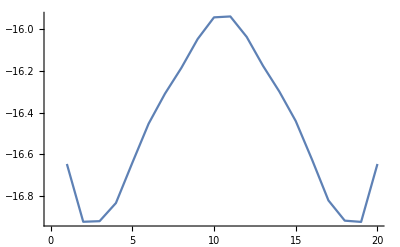

```mathematica
energytable[[-1]]//ListLinePlot
```

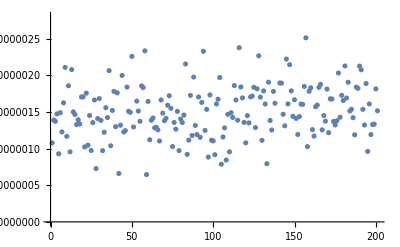

```mathematica
(*Maximum difference between distances between states in string (should be near zero)*)
Table[(Max[#]-Min[#])&[Norm/@(postable[[k]]//Differences)],{k,1,Length[postable]}]//ListPlot
```

```mathematica
(*Rate of change*)
Table[distance[postable[[j]][[k]],postable[[j]][[k+1]]],{k,1,Length[postable[[1]]]-1},{j,1,nIters}][[50]]//ListPlot
```

```mathematica
Manipulate[ListPlot[Table[distance[postable[[j]][[k]],postable[[j]][[k+1]]],{k,1,Length[postable[[1]]]-1}],PlotRange->Full],{j,1,nIters,1}]
```

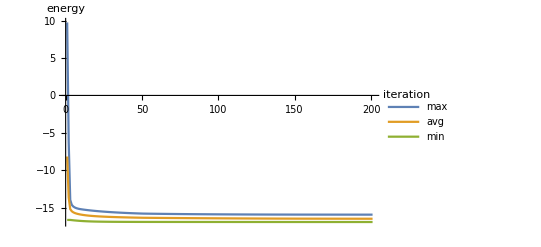

```mathematica
energyplot=ListPlot[{Max/@energytable,Mean/@energytable,Min/@energytable},PlotRange->{Automatic,Full},Joined->True,AxesLabel->{"iteration","energy"},PlotLegends->{"max","avg","min"}]
```

```mathematica
animation=ParallelTable[showPhi[postable[[iter]]],{iter,1,nIters,1}];
```

```mathematica
ListAnimate[animation]
```

```mathematica
(*Export["moving_particles.gif",animation,ImageSize->{60*3,60*3}]*)
```

moving_particles.gif

```mathematica
(*Export["energy_vs_iteration.png",energyplot]*)
```

energy_vs_iteration.png

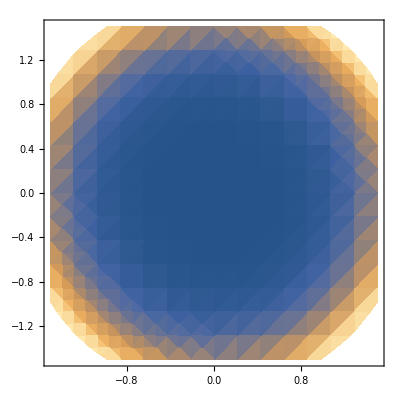

```mathematica
DensityPlot[((x/2)^2+(y/2)^2)^3,{x,-1.5,1.5},{y,-1.5,1.5}]
```

```mathematica
((x/2)^2+(y/2)^2)^10/.{x->2.5,y->0}
```

86.7362

```mathematica
D[((x/2)^2+(y/2)^2)^10,x]
```

5 x (x^2/4+y^2/4)^9

```mathematica
D[((x/1)^2+(y/1)^2)^10,x]
```

20 x (x^2+y^2)^9

```mathematica
D[r^-4-2 r^-2/.{r->√(x^2+y^2)},x]//FullSimplify
```

(4 x (-1+x^2+y^2))/((x^2+y^2)^3)